```mathematica
(*Вариант 10*)
(*Корнеенко Егор*) 
(*Задание 1*)
 (*n=6*)

f[x_]=(Sinh[√(x^2+x + 5)]+π)/(√(3 x^8+11 x^4+33))
```

(π+Sinh[√(5+x+x^2)])/(√(33+11 x^4+3 x^8))

```mathematica
a=0; b=6; n=6; h=(b-a)/n;
data = N[Table[{a+i*h, f[a+i*h]}, {i,0,n}]](*посчитаем значения функции на отрезке [0,n], разделя отрезок на равные части]*)
```

{{0.,1.35195},{1.,1.48099},{2.,0.540904},{3.,0.236911},{4.,0.173183},{5.,0.173726},{6.,0.212533}}

```mathematica
Buff[x_]=1;
 L[x_]=0;
```

```mathematica
(*строим интерполяционный многочлен Лагранжа*)
sum=0;
For[i=1, i<=n+1, i++,
proizv=1;
Buff[x_]=1;
For[j=1, j<=n+1, j++,
If[
i==j, Continue[];
];
Buff[x_]=Buff[x]*(x-data[[j,1]]);
proizv=proizv*(data[[i,1]]-data[[j,1]]);
];
summand = data[[i,2]]/proizv;
L[x_]=(L[x]+Buff[x]*summand);
]
```

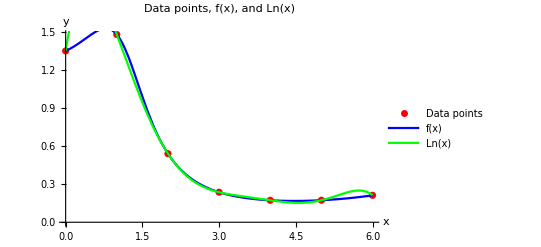

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->Blue,PlotLegends->{"f(x)"}],Plot[L[x],{x,0,n},PlotStyle->Green,PlotLegends->{"Ln(x)"}],AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and Ln(x)",ImageSize->Large]
```

```mathematica
Array[dif, {n+1, n+1}, {0,0}];(*создаем массив для конечных разностей*)
```

```mathematica
For[k=1, k<=n, k++,
For[i=n, i>=n-k, i--, dif[i,k]=""](*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)
];
```

```mathematica
For[i=0, i<=n,i++,dif[i,0]=data[[i+1,2]]];(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
```

```mathematica
For[k=1, k<=n,k++,(*Считаем конечные разности*)
For[i=0, i<=n-k, i++,
dif[i,k]=dif[i+1, k-1]-dif[i,k-1]
]
];
```

```mathematica
tab=Array[dif, {n+1, n+1},{0,0}];
```

```mathematica
PaddedForm[TableForm[tab], {6,5}] (*получаем таблицу конечных разностей*)
```

1.35195 |  0.12903 | -1.06911 |  1.70520 | -2.10103 |  2.32086 | -2.39069
 1.48099 | -0.94008 |  0.63609 | -0.39582 |  0.21983 | -0.06984 | 
 0.54090 | -0.30399 |  0.24027 | -0.17600 |  0.14999 |  | 
 0.23691 | -0.06373 |  0.06427 | -0.02601 |  |  | 
 0.17318 |  0.00054 |  0.03826 |  |  |  | 
 0.17373 |  0.03881 |  |  |  |  | 
 0.21253 |  |  |  |  |  |

```mathematica
t=(x-a)/h; pn1[x_]=dif[0,0]; p[t_]=1(*строим первый интерполяционный многочлен Ньютона pn1(x)*)
```

1

```mathematica
For[k=1,k<=n, k++,
p[t_]=p[t]*(t-k+1);
pn1[x_]=pn1[x]+dif[0,k]/(k!)*p[t]
]
```

```mathematica
pn1[x]
```

1.35195+0.129032 x-0.534557 (-1+x) x+0.284201 (-2+x) (-1+x) x-0.0875428 (-3+x) (-2+x) (-1+x) x+0.0193405 (-4+x) (-3+x) (-2+x) (-1+x) x-0.00332041 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x

```mathematica
pn1[x_]=Simplify[pn1[x]]
```

1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6

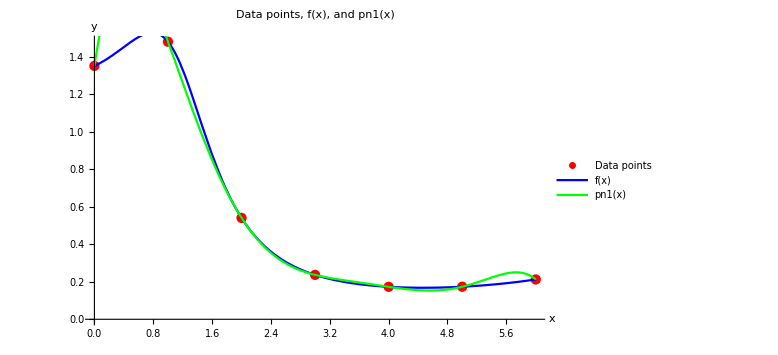

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->Blue,PlotLegends->{"f(x)"}],Plot[pn1[x],{x,0,n},PlotStyle->Green,PlotLegends->{"pn1(x)"}],AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and pn1(x)",ImageSize->Large]
```

```mathematica
Np[x_]=InterpolatingPolynomial[data, x](*строим интерполяционный многочлен Ньютона Np(x) с помощью функции InterpolatingPolynomial*)
```

0.212533+(-6.+x) (-0.189904+(0.0605926+(0.0621898+(-0.0174038+(0.0126996-0.00332041 (-2.+x)) (-5.+x)) (-1.+x)) (-3.+x)) (0.+x))

```mathematica
Np[x_]=Simplify[Np[x]]
```

1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6

```mathematica
f[2.4316](*Считаем значения всех фугкций/многочленов в точке 2.4316*)
L[2.4316]
pn1[2.4316]
Np[2.4316]
```

0.350875

0.343952

0.343952

0.343952

```mathematica
(*n=10*)
a = 0; b = 6; n = 10; h = (b - a)/n; 
data = N[Table[{a + i*h, f[a + i*h]}, {i, 0, n}]]
DataForSplain=data
```

{{0.,1.35195},{0.6,1.50591},{1.2,1.33212},{1.8,0.685663},{2.4,0.360695},{3.,0.236911},{3.6,0.187258},{4.2,0.169776},{4.8,0.170404},{5.4,0.184714},{6.,0.212533}}

{{0.,1.35195},{0.6,1.50591},{1.2,1.33212},{1.8,0.685663},{2.4,0.360695},{3.,0.236911},{3.6,0.187258},{4.2,0.169776},{4.8,0.170404},{5.4,0.184714},{6.,0.212533}}